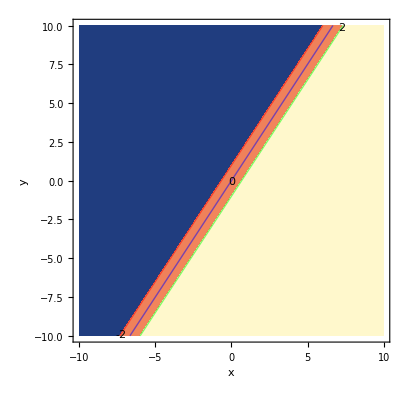
{{Null -Graphics-},{□}}

```mathematica
(*Define the function f(x,y)*){{f[x_,y_]:=3 x-2 y

(*Create level curves for c=-2,0,and 2*)
ContourPlot[f[x,y],{x,-10,10},{y,-10,10},Contours->{-2,0,2},ContourLabels->True,ContourStyle->{Red,Blue,Green},FrameLabel->{"x","y"},PlotLegends->"Expressions"]}, {□}}
```

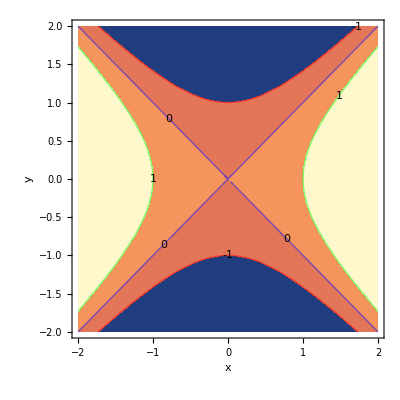

```mathematica
(*Define the function f(x,y)*)f[x_,y_]:=x^2-y^2

(*Create level curves for c=-1,0,and 1*)
ContourPlot[f[x,y],{x,-2,2},{y,-2,2},Contours->{-1,0,1},ContourLabels->True,ContourStyle->{Red,Blue,Green},FrameLabel->{"x","y"},PlotLegends->"Expressions"]
```

```mathematica
f[x_]:=1/(x^2-4)

domain=Reduce[Denominator[f[x]]!=0,x,y Reals]
range=FunctionRange[{f[x],x>-Infinity&&x<Infinity},y,y]

Print["The domain of the function f(x) is:",domain]
Print["The range of the function f(x) is:",range]
```

x<-2||-2<x<2||x>2

-4+x^2≠0

The domain of the function f(x) is:x<-2||-2<x<2||x>2

The range of the function f(x) is:-4+x^2≠0

```mathematica
f[x_,y_]:=sqrt[9-x^2 - Y^2]

domain=Reduce[{f[x,y]>=0},{x,y}]
region=ImplicitRegion[x^2+y^2<=4,{x,y}]
range=FullSimplify[Minimize[{f[x,y],x>=0,y>=0},{x,y}],Assumptions->{x,y}∈Reals]

Print["Domain of f(x, y): ",domain]
Print["The range of the function f(x, y) is:",range]
```

The range of the function f(x, y) is:NMaxValue[{sqrt[9-x^2-Y^2],{x,y}∈ImplicitRegion[x^2+y^2≤4,{x,y}]},{x,y}]

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{sqrt[9-x^2-Y^2]≥0},{x,y}]

ImplicitRegion[x^2+y^2≤4,{x,y}]

Minimize[{sqrt[9-x^2-Y^2],x≥0,y≥0},{x,y}]

Domain of f(x, y): Reduce[{sqrt[9-x^2-Y^2]≥0},{x,y}]

The range of the function f(x, y) is:Minimize[{sqrt[9-x^2-Y^2],x≥0,y≥0},{x,y}]

The range of the function f(x, y) is:6.

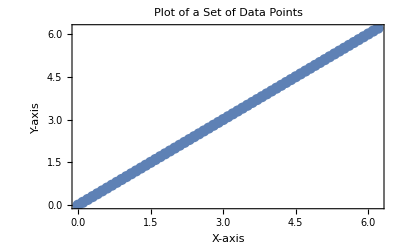

```mathematica
(*Generate a sample set of data points*)data=Table[{x,x},{x,0,2 Pi,0.1}];

(*Plot the data points*)
ListPlot[data,PlotStyle->PointSize[0.02],PlotRange->All,Frame->True,FrameLabel->{"X-axis","Y-axis"},PlotLabel->"Plot of a Set of Data Points"]
```

```mathematica
Plot3D[(x^2-y^2)/(x^2+y^2),{x,-100,100},{y,-100,100},PlotRange->{-100,100},AxesLabel->{"x","y","f(x, y)"},PlotStyle->Opacity[0.7],MeshFunctions->{#3&},MeshStyle->Thick]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[x^2+y^2]},{x,-100,100},{y,-100,100},PlotRange->{{0,50},{0,50},{0,50}},AxesLabel->{"x","y","z"},MeshFunctions->{#3&},MeshStyle->{{Thick,Red},{Thick,Blue}},BoxRatios->{1,1,1}]
```

-Graphics3D-